## Example of KL divergence measuring clumpiness

First create a nice spiky distribution - this one has 10 “streams”

```mathematica
Clear[spikyDist]
```

The function “MixtureDistribution” makes a sum of normal distributions with random positions and weights but in this case all the same width

```mathematica
(*spikyDist =MixtureDistribution[RandomReal[{0,1},10],Table[NormalDistribution[RandomReal[{-5,5}],0.1],{i,1,10}]]*)
```

Here I freeze the distribution, so that it doesn’t keep regenerating a new one

```mathematica
spikyDist =MixtureDistribution[{0.38174541586280086,0.8005643054256613,0.17576919061598972,0.9098835720952063,0.9015093054785912,0.3997673951005183,0.3248768581708732,0.6135124567486943,0.5231136262784264,0.3192552522927914},{NormalDistribution[-2.0044394996939694,0.1],NormalDistribution[2.193733320515694,0.1],NormalDistribution[1.6822767019539064,0.1],NormalDistribution[2.785894856245946,0.1],NormalDistribution[2.7394525365956,0.1],NormalDistribution[0.3629336482053489,0.1],NormalDistribution[1.6208850719907382,0.1],NormalDistribution[-3.118058823154943,0.1],NormalDistribution[-4.5106415851510455,0.1],NormalDistribution[-1.5595948007090694,0.1]}];
```

```mathematica
CDF[spikyDist,5]
```

1.

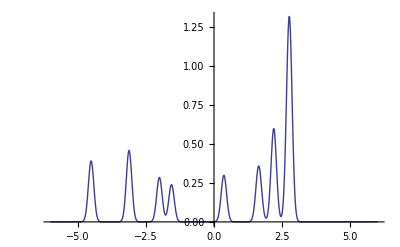

```mathematica
Plot[PDF[spikyDist,x],{x,-6,6},PlotRange->All]
```

“Observe” some points drawn from this distribution and find their mean and stdev

I’m assuming we get about 10 points per stream on average

```mathematica
observedPoints=RandomVariate[spikyDist,100];
```

```mathematica
muObs=Mean[observedPoints]
sigObs=StandardDeviation[observedPoints]
```

0.165958

2.72206

Create a “trial” distribution to compare to, using the observed mean and stdev

```mathematica
trialDist=NormalDistribution[muObs,sigObs]
```

NormalDistribution[0.165958,2.72206]

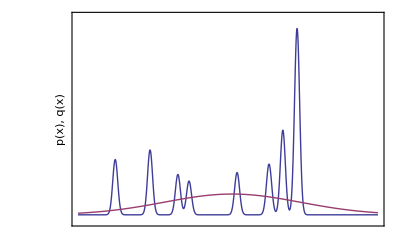

```mathematica
p11=Plot[{PDF[spikyDist,x],PDF[trialDist,x]},{x,-6,6},PlotStyle->Thick,PlotRange->{-.05,1.4},FrameTicks->False,FrameLabel->{" ","p(x), q(x)"},Frame->True,FrameStyle->Directive[FontFamily->"Helvetica",FontSize->16]]
```

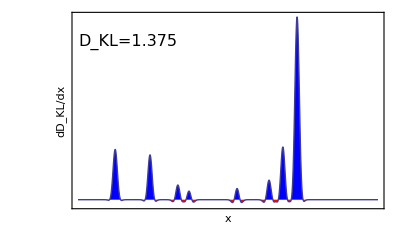

```mathematica
p21=Plot[PDF[spikyDist,x] Log[PDF[spikyDist,x]/PDF[trialDist,x]],{x,-6,6},PlotRange->{-0.1,3.5},Filling->Axis,FillingStyle->{Red,Blue},FrameTicks->False,FrameLabel->{"x","dD_KL/dx"},Frame->True,FrameStyle->Directive[FontFamily->"Helvetica",FontSize->16],Epilog->Text[Style["D_KL=1.375",FontFamily->"Helvetica",FontSize->16,TextAlignment->Left],{-4,3}]]
```

```mathematica
NIntegrate[PDF[spikyDist,x] Log[PDF[spikyDist,x]/PDF[trialDist,x]],{x,-6.,6.}]
```

1.37527

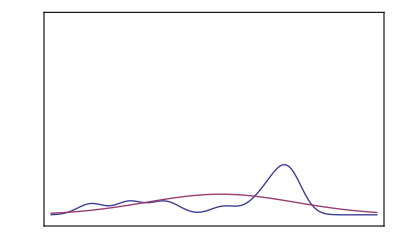

```mathematica
p12=Plot[{PDF[smoothDist,x],PDF[trialDistSmooth,x]},{x,-6,6},FrameLabel->{" "," "},PlotStyle->Thick,PlotRange->{-.05,1.4},FrameTicks->False,Frame->True,FrameStyle->Directive[FontFamily->"Helvetica",FontSize->16]]
```

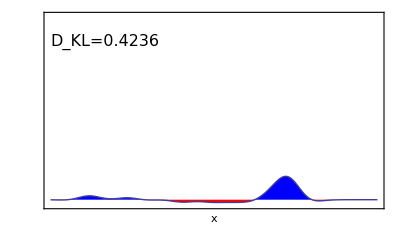

```mathematica
p22=Plot[PDF[smoothDist,x] Log[PDF[smoothDist,x]/PDF[trialDistSmooth,x]],{x,-6,6},PlotRange->{-0.1,3.5},Filling->Axis,FillingStyle->{Red,Blue},FrameTicks->False,FrameLabel->{"x"," "},Frame->True,FrameStyle->Directive[FontFamily->"Helvetica",FontSize->16],Epilog->Text[Style["D_KL=0.4236",FontFamily->"Helvetica",FontSize->16,TextAlignment->Left],{-4,3}]]
```

```mathematica
NIntegrate[PDF[smoothDist,x] Log[PDF[smoothDist,x]/PDF[trialDistSmooth,x]],{x,-6,6}]
```

0.423652

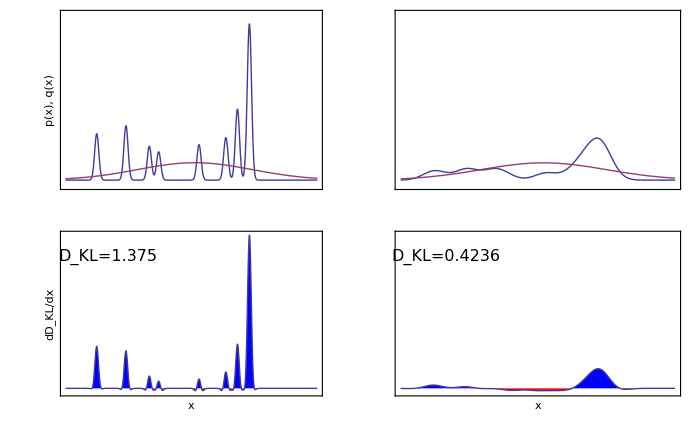

```mathematica
GraphicsGrid[{{p11,p12},{p21,p22}}]
```

Make the “observed” distribution - the empirical one that fits all the points

Note that I was somewhat sneaky here and chose a bandwidth for the Gaussian smoothing kernel equal to the width of all the peaks in the parent distribn.

```mathematica
obsvDist=SmoothKernelDistribution[observedPoints,0.1]
```

DataDistribution[«SmoothKernel»,{100}]

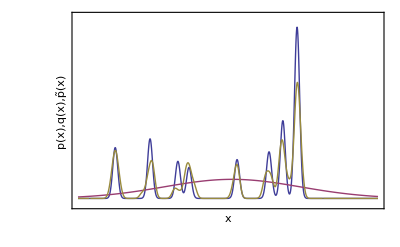

```mathematica
p1=Plot[{PDF[spikyDist,x],PDF[trialDist,x],PDF[obsvDist,x]},{x,-6,6},PlotRange->{-.05,1.4},PlotStyle->Thick,Frame->True,FrameTicks->None,FrameLabel->{"x","p(x),q(x),p̃(x)"},FrameStyle->Directive[FontFamily->"Helvetica",FontSize->16]]
```

Calculate the KL divergence that compares the true distribution to the trial

This is a plot of the things we are comparing:

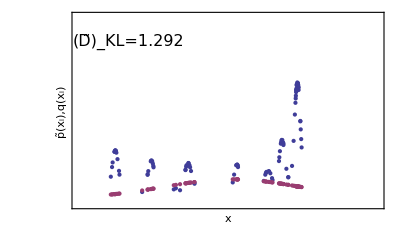

```mathematica
p2=ListPlot[{Transpose[{observedPoints,PDF[obsvDist,observedPoints]}],Transpose[{observedPoints,PDF[trialDist,observedPoints]}]},PlotRange->{{-6,6},{-.05,1.4}},Frame->True,FrameLabel->{"x","p̃(x_i),q(x_i)"},FrameStyle->Directive[FontFamily->"Helvetica",FontSize->16],FrameTicks->None,Epilog->Text[Style["(D̃)_KL=1.292",FontFamily->"Helvetica",FontSize->16,TextAlignment->Left],{-4,1.2}]]
```

```mathematica
spikyKLDivergence=Total[Log[PDF[obsvDist,observedPoints]/PDF[trialDist,observedPoints]]]/Length[observedPoints]
```

1.29208

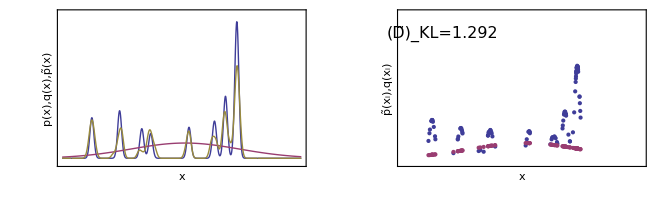

```mathematica
GraphicsGrid[{{p1,p2}}]
```

Take the spiky parent distribution and broaden all the Gaussians by a factor of 10 to “smooth” it

```mathematica
smoothDist=MixtureDistribution[{0.38174541586280086,0.8005643054256613,0.17576919061598972,0.9098835720952063,0.9015093054785912,0.3997673951005183,0.3248768581708732,0.6135124567486943,0.5231136262784264,0.3192552522927914},{NormalDistribution[-2.0044394996939694,0.5],NormalDistribution[2.193733320515694,0.5],NormalDistribution[1.6822767019539064,0.5],NormalDistribution[2.785894856245946,0.5],NormalDistribution[2.7394525365956,0.5],NormalDistribution[0.3629336482053489,0.5],NormalDistribution[1.6208850719907382,0.5],NormalDistribution[-3.118058823154943,0.5],NormalDistribution[-4.5106415851510455,0.5],NormalDistribution[-1.5595948007090694,0.5]}];
```

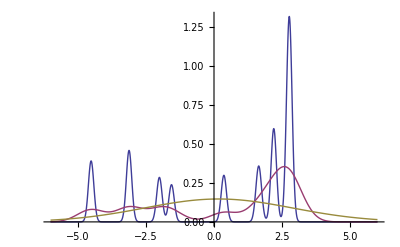

```mathematica
Plot[{PDF[spikyDist,x],PDF[smoothDist,x],PDF[trialDist,x]},{x,-6,6},PlotRange->All]
```

Draw from this distribution and find the empirical and trial distributions

```mathematica
observedPointsSmooth= RandomVariate[smoothDist,100];
muObsSmooth=Mean[observedPointsSmooth]
sigObsSmooth=StandardDeviation[observedPointsSmooth]
```

0.252425

2.7438

Note that I am now pretending I’m dumb and picked the same smoothing kernel as before to construct the observed distribution

```mathematica
obsvDistSmooth=SmoothKernelDistribution[observedPointsSmooth,0.1];
trialDistSmooth=NormalDistribution[muObsSmooth,sigObsSmooth];
```

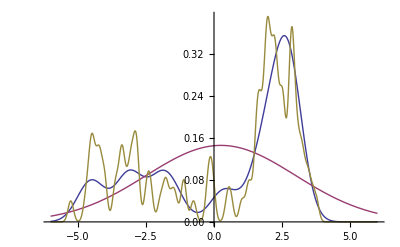

```mathematica
Plot[{PDF[smoothDist,x],PDF[trialDistSmooth,x],PDF[obsvDistSmooth,x]},{x,-6,6},PlotRange->All]
```

The KL divergence of the “smoothed” distribution on the observed points is lower

```mathematica
smoothKLDivergence = Total[Log[PDF[obsvDistSmooth,observedPointsSmooth]/PDF[trialDistSmooth,observedPointsSmooth]]]
```

65.1262

You should still get a lower KL divergence if you pick the “right” (best) kernel size (in fact, it should be lower than the above since you are smoothing more)

```mathematica
obsvDistSmooth2=SmoothKernelDistribution[observedPointsSmooth,0.5];
```

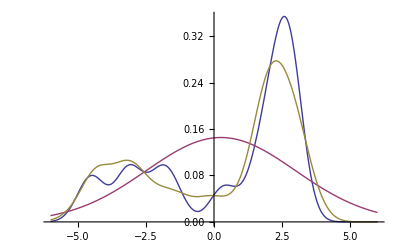

```mathematica
Plot[{PDF[smoothDist,x],PDF[trialDistSmooth,x],PDF[obsvDistSmooth2,x]},{x,-6,6},PlotRange->All]
```

```mathematica
smoothKLDivergence2 = Total[Log[PDF[obsvDistSmooth2,observedPointsSmooth]/PDF[trialDistSmooth,observedPointsSmooth]]]
```

44.1423

But, if you pick a shorter smoothing length you can get a larger KLD:

```mathematica
obsvDistSmooth3=SmoothKernelDistribution[observedPointsSmooth,0.01];
```

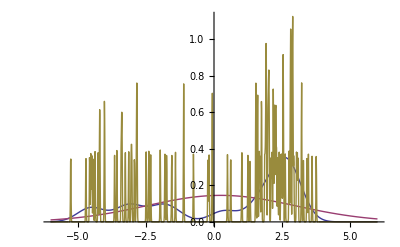

```mathematica
Plot[{PDF[smoothDist,x],PDF[trialDistSmooth,x],PDF[obsvDistSmooth3,x]},{x,-6,6},PlotRange->All]
```

```mathematica
smoothKLDivergence3 = Total[Log[PDF[obsvDistSmooth3,observedPointsSmooth]/PDF[trialDistSmooth,observedPointsSmooth]]]
```

172.535